```mathematica
d=-Graphics3D-;
cl=MorphologicalComponents[d] ;
f:=#&;
f1=Clip[(cl/.{2->0,3->0}),{0,1}]//Image3D;
f2=Clip[(cl/.{1->0,3->0}),{0,1}]//Image3D;
f3=Clip[(cl/.{1->0,2->0}),{0,1}]//Image3D;
features={f1,f2,f3}
{ImageMeasurements[f1,"TotalIntensity"]//N,ImageMeasurements[f2,"TotalIntensity"]//N,ImageMeasurements[f3,"TotalIntensity"]//N}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

{4089.,6579.,4089.}

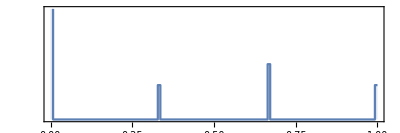

{RGBColor[{0.7725490196078432, 0.8509803921568627, 0.7333333333333333}],RGBColor[{0.8117647058823529, 0.22745098039215686, 0.8549019607843137}],RGBColor[{0.3764705882352941, 0.6313725490196078, 0.5843137254901961}]}

```mathematica
normalized=cl//Image3D//ImageAdjust;
Export[NotebookDirectory[]<>"disk.raw",Flatten@ImageData[normalized,"Byte"],{"Binary","Byte"}];
ImageHistogram[normalized]
colorized=cl//Colorize;
chartcolors={PixelValue[colorized,{10,20,30}]//RGBColor,PixelValue[colorized,{20,20,20}]//RGBColor,PixelValue[colorized,{30,20,10}]//RGBColor}
```

```mathematica
disks1=Show[colorized,Boxed->False,ViewPoint->Left]
Export[NotebookDirectory[]<>"disks_left.png",disks1];
disks2=Show[colorized,Boxed->False,ViewPoint->Right]
Export[NotebookDirectory[]<>"disks_right.png",disks2];
```

-Graphics3D-

-Graphics3D-

```mathematica
(* left *)
list=Image3DSlices[d,All,3];
count=Length[list]
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
d3a=Image3D[list3];
d3=ImageRotate[d3a,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&
```

41

-Graphics3D-

```mathematica
(* right *)
list=Reverse@Image3DSlices[d,All,3];
count=Length[list]
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
d6a=Image3D[Reverse[list3]];
d6=ImageRotate[d6a,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&
```

41

-Graphics3D-

```mathematica
(*opacity=ImageApply[f[#]&,d];
diff=ImageSubtract[opacity,d3]//ImageAdjust;*)
(*r=ImageApply[{1,1,1,#2}*List@@rgbafunction[#1]&,{d,diff}]//Image3D[#,ColorSpace->"RGB"]&*)
dog1=ImageSubtract[GaussianFilter[opacity,2],GaussianFilter[opacity,4]];
dog2=ImageSubtract[GaussianFilter[opacity,{2,Sqrt[2]/8.*2}],GaussianFilter[opacity,{4,Sqrt[2]/8.*4}]]
Export[NotebookDirectory[]<>"disks_saliency.png",dog2];
```

{0.450036,0.381473,0.16849}

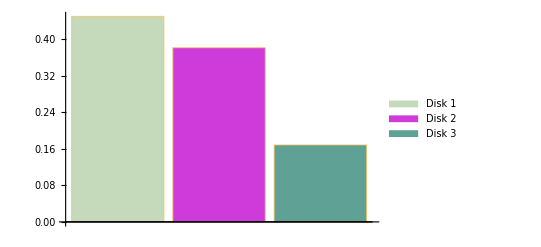

{0.0796755,0.126683,0.0796755}

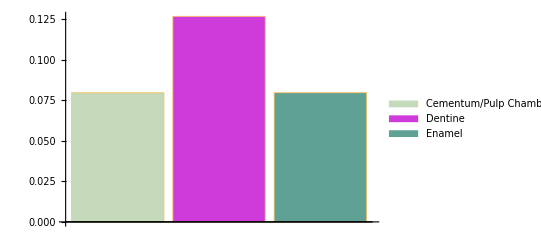

{0.441833,0.387714,0.170453}

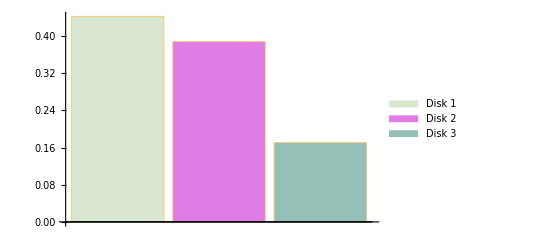

```mathematica
visibility=Table[ImageApply[#*#2&,{d3,features[[i]]}]//ImageMeasurements[#,"TotalIntensity"]/ImageMeasurements[d3,"TotalIntensity"]&,{i,Length[features]}]
chart1=BarChart[visibility,ChartLegends->{"Disk 1","Disk 2","Disk 3"},ChartStyle->chartcolors]
dog=ImageAdjust[dog2];
saliency=Table[ImageApply[#*#2&,{dog,features[[i]]}]//ImageMeasurements[#,"TotalIntensity"]/ImageMeasurements[dog,"TotalIntensity"]&,{i,Length[features]}]
BarChart[saliency,ChartLegends->{"Cementum/Pulp Chamber","Dentine","Enamel"},ChartStyle->chartcolors]
ss=ImageApply[#*#2&,{dog,d3}];
vs=Table[ImageApply[#*#2*#3&,{dog,features[[i]],d3}]//ImageMeasurements[#,"TotalIntensity"]/ImageMeasurements[ss,"TotalIntensity"]&,{i,Length[features]}]
chart2=BarChart[vs,ChartLegends->{"Disk 1","Disk 2","Disk 3"},ChartStyle->(chartcolors//Lighter)]
Export[NotebookDirectory[]<>"disks_visibility_chart_left.png",chart1];
Export[NotebookDirectory[]<>"disks_saliency_chart_left.png",chart2];
```

{0.16849,0.381473,0.450036}

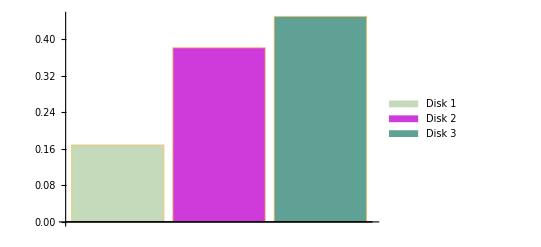

{0.0796755,0.126683,0.0796755}

-Graphics-

{0.170453,0.387714,0.441833}

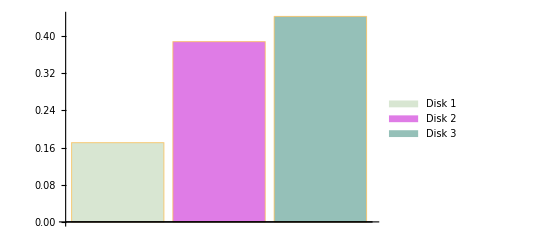

```mathematica
visibility=Table[ImageApply[#*#2&,{d6,features[[i]]}]//ImageMeasurements[#,"TotalIntensity"]/ImageMeasurements[d6,"TotalIntensity"]&,{i,Length[features]}]
chart1=BarChart[visibility,ChartLegends->{"Disk 1","Disk 2","Disk 3"},ChartStyle->chartcolors]
dog=ImageAdjust[dog2];
saliency=Table[ImageApply[#*#2&,{dog,features[[i]]}]//ImageMeasurements[#,"TotalIntensity"]/ImageMeasurements[dog,"TotalIntensity"]&,{i,Length[features]}]
BarChart[saliency,ChartLegends->{"Cementum/Pulp Chamber","Dentine","Enamel"},ChartStyle->chartcolors]
ss=ImageApply[#*#2&,{dog,d6}];
vs=Table[ImageApply[#*#2*#3&,{dog,features[[i]],d6}]//ImageMeasurements[#,"TotalIntensity"]/ImageMeasurements[ss,"TotalIntensity"]&,{i,Length[features]}]
chart2=BarChart[vs,ChartLegends->{"Disk 1","Disk 2","Disk 3"},ChartStyle->(chartcolors//Lighter)]
Export[NotebookDirectory[]<>"disks_visibility_chart_right.png",chart1];
Export[NotebookDirectory[]<>"disks_saliency_chart_right.png",chart2];
```

```mathematica
lab=ColorConvert[colorized,"LAB"];
dog3=ImageSubtract[GaussianFilter[lab,{2,Sqrt[2]/8.*2}],GaussianFilter[lab,{4,Sqrt[2]/8.*4}]]
```

-Graphics3D-

```mathematica
cs=ColorSeparate[ColorConvert[dog3,"LAB"]]
ColorSeparate[ColorConvert[colorized,"LAB"]]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
dog4=ImageApply[Norm[#]&,dog3]
```

-Graphics3D-

{0.450036,0.381473,0.16849}

-Graphics-

{0.139148,0.254798,0.10676}

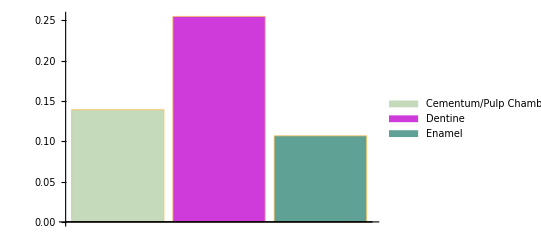

{0.415612,0.456202,0.128186}

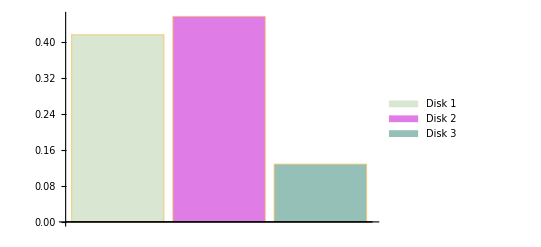

```mathematica
visibility=Table[ImageApply[#*#2&,{d3,features[[i]]}]//ImageMeasurements[#,"TotalIntensity"]/ImageMeasurements[d3,"TotalIntensity"]&,{i,Length[features]}]
chart1=BarChart[visibility,ChartLegends->{"Disk 1","Disk 2","Disk 3"},ChartStyle->chartcolors]
dog=ImageAdjust[dog4];
saliency=Table[ImageApply[#*#2&,{dog,features[[i]]}]//ImageMeasurements[#,"TotalIntensity"]/ImageMeasurements[dog,"TotalIntensity"]&,{i,Length[features]}]
BarChart[saliency,ChartLegends->{"Cementum/Pulp Chamber","Dentine","Enamel"},ChartStyle->chartcolors]
ss=ImageApply[#*#2&,{dog,d3}];
vs=Table[ImageApply[#*#2*#3&,{dog,features[[i]],d3}]//ImageMeasurements[#,"TotalIntensity"]/ImageMeasurements[ss,"TotalIntensity"]&,{i,Length[features]}]
chart2=BarChart[vs,ChartLegends->{"Disk 1","Disk 2","Disk 3"},ChartStyle->(chartcolors//Lighter)]
Export[NotebookDirectory[]<>"disks_visibility_chart_left.png",chart1];
Export[NotebookDirectory[]<>"disks_saliency_chart_left.png",chart2];
```

{0.16849,0.381473,0.450036}

-Graphics-

{0.139148,0.254798,0.10676}

-Graphics-

{0.177332,0.484213,0.338456}

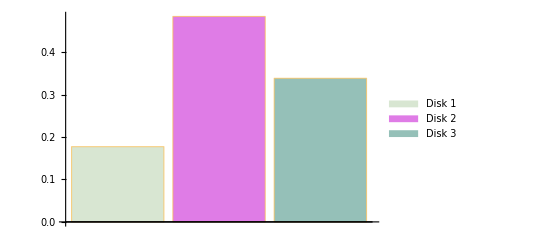

```mathematica
visibility=Table[ImageApply[#*#2&,{d6,features[[i]]}]//ImageMeasurements[#,"TotalIntensity"]/ImageMeasurements[d6,"TotalIntensity"]&,{i,Length[features]}]
chart1=BarChart[visibility,ChartLegends->{"Disk 1","Disk 2","Disk 3"},ChartStyle->chartcolors]
dog=ImageAdjust[dog4];
saliency=Table[ImageApply[#*#2&,{dog,features[[i]]}]//ImageMeasurements[#,"TotalIntensity"]/ImageMeasurements[dog,"TotalIntensity"]&,{i,Length[features]}]
BarChart[saliency,ChartLegends->{"Cementum/Pulp Chamber","Dentine","Enamel"},ChartStyle->chartcolors]
ss=ImageApply[#*#2&,{dog,d6}];
vs=Table[ImageApply[#*#2*#3&,{dog,features[[i]],d6}]//ImageMeasurements[#,"TotalIntensity"]/ImageMeasurements[ss,"TotalIntensity"]&,{i,Length[features]}]
chart2=BarChart[vs,ChartLegends->{"Disk 1","Disk 2","Disk 3"},ChartStyle->(chartcolors//Lighter)]
Export[NotebookDirectory[]<>"disks_visibility_chart_right.png",chart1];
Export[NotebookDirectory[]<>"disks_saliency_chart_right.png",chart2];
```

```mathematica
ColorConvert[chartcolors,"LCH"]//InputForm
```

{LCHColor[0.8457525303878418, 0.1662884134396095, 0.36521314399007476], LCHColor[0.5313118127465906, 0.8805289444634591, 0.9004439699369401], 
 LCHColor[0.6163180448292418, 0.23979187569097918, 0.5042058574060774]}

```mathematica
ColorConvert[chartcolors,"LAB"]//InputForm
```

{LABColor[0.8457525303878418, -0.11013544991738733, 0.12458739549311226], LABColor[0.5313118127465906, 0.7138038690777071, -0.5155727480459271], 
 LABColor[0.6163180448292418, -0.23970815206657725, -0.00633604610342231]}

```mathematica
chartcolors//InputForm
```

{RGBColor[{0.7725490196078432, 0.8509803921568627, 0.7333333333333333}], RGBColor[{0.8117647058823529, 0.22745098039215686, 0.8549019607843137}], 
 RGBColor[{0.3764705882352941, 0.6313725490196078, 0.5843137254901961}]}

```mathematica
ImageMultiply[d,dog2]
```

-Graphics3D-

```mathematica
Table[ImageApply[#*#2*#3&,{dog,features[[i]],d3}],{i,Length[features]}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Table[ImageApply[#*#2*#3&,{dog,features[[i]],d6}],{i,Length[features]}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}